# Alkali atom magnetic field shifts and branching ratios

The math presented here relies heavily on https://steck.us/alkalidata/cesiumnumbers.1.6.pdf

#### Declare constants

```mathematica
ℏ = 1; 
h = 2*Pi*ℏ; 
μB = 1.399624604; 
gI = -0.00039885395; 
gJGs = 1.334; 
gJEs = 2.00254032; 
totIGs = 7/2; 
totIEs = 7/2; 
totJGs = 1/2; 
totJEs = 3/2; 
AhfsGs=2.2981579425  10^3; (* in MHz *)
BhfsGs=0;
ChfsGs=0;
AhfsEs=50.28827; (* in MHz *)
BhfsEs=-0.4934 ; (* in MHz *)
ChfsEs=0.560 10^-3;(* in MHz *)
```

#### Solve ground state

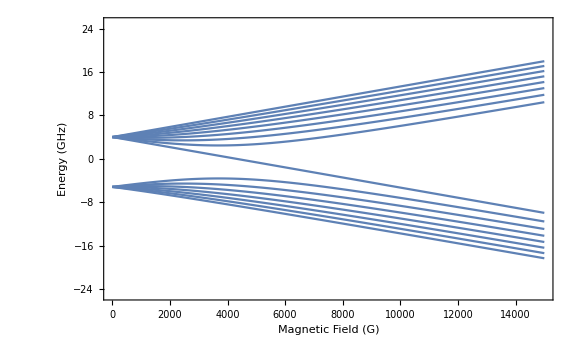

```mathematica
nStatesGs=(2totIGs+1)*(2totJGs+1);
IzGs=DiagonalMatrix[Table[mi,{mi,-totIGs,totIGs}]];
JzGs=DiagonalMatrix[Table[mj,{mj,-totJGs,totJGs}]];
IplusGs=DiagonalMatrix[Table[√(totIGs(totIGs+1)-mi(mi+1)),{mi,-totIGs,totIGs-1}],-1];
IminusGs=Transpose[IplusGs];
JplusGs=DiagonalMatrix[Table[√(totJGs(totJGs+1)-mj(mj+1)),{mj,-totJGs,totJGs-1}],-1];
JminusGs=Transpose[JplusGs];
JxGs=1/2(JplusGs+JminusGs);
JyGs=1/(2I)(JplusGs-JminusGs);
IxGs=1/2(IplusGs+IminusGs);
IyGs=1/(2I)(IplusGs-IminusGs);
JidGs=IdentityMatrix[2totJGs+1];
IidGs=IdentityMatrix[2totIGs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzGs=OpOuter[JidGs,IzGs];
JzGs=OpOuter[JzGs,IidGs];
IxGs=OpOuter[JidGs,IxGs];
JxGs=OpOuter[JxGs,IidGs];
IyGs=OpOuter[JidGs,IyGs];
JyGs=OpOuter[JyGs,IidGs];
HhfsSimpleGs=AhfsGs(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs);
HhfsHigherOrderGs=If[Abs[BhfsGs]>0,BhfsGs((3(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+3/2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)-totIGs(totIGs+1)totJGs(totJGs+1))/(2totIGs(2totIGs-1)totJGs(2totJGs-1)))+ChfsGs(10(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^3+20(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)^2+2(IxGs.JxGs+IyGs.JyGs+IzGs.JzGs)(totIGs(totIGs+1)+totJGs(totJGs+1)+3-3totIGs(totIGs+1)totJGs(totJGs+1))-5totIGs(totIGs+1)totJGs(totJGs+1))/(totIGs(totIGs-1)(2totIGs-1)totJGs(totJGs-1)(2totJGs-1)),0];
HzeemanGs=μB(gJGsJzGs+gIIzGs)Bz;
{evalsGs,evecsGs}=Eigensystem[HzeemanGs+HhfsSimpleGs];
evecsGs=Simplify[Table[evecsGs[[ii]]/Sqrt[Total[Conjugate[evecsGs[[ii]]].evecsGs[[ii]]]],{ii,1,nStatesGs}],Bz∈Reals];
energiesGs=Simplify[Table[Conjugate[evecsGs[[ii]]].(HzeemanGs+HhfsSimpleGs+HhfsHigherOrderGs).evecsGs[[ii]],{ii,1,nStatesGs}],Bz∈Reals];
mIlistGs=Table[IzGs[[ii,ii]],{ii,1,nStatesGs}];mJlistGs=Table[JzGs[[ii,ii]],{ii,1,nStatesGs}];FlistGs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mFlistGs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]];mImJtoFmFGs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIGs,mIlistGs[[ii]]},{totJGs,mJlistGs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIGs-totJGs,totIGs+totJGs}]],{ii,1,nStatesGs}]]];evecsHighFieldGs=Chop[N[evecsGs/.Bz->10^10],10^-4];
evecsLowFieldGs=Chop[N[evecsGs/.Bz->0],10^-4];
IJcomponentsGs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistGs[[indmax]], mJlistGs[[indmax]]}
];
FmFcomponentsGs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFGs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistGs[[indmax]],mFlistGs[[indmax]]}];
{mIhighfieldGs,mJhighfieldGs}=Transpose[Table[IJcomponentsGs[evecsHighFieldGs[[ii]]],{ii,1,nStatesGs}]];
{FlowfieldGs,mFlowfieldGs}=Transpose[Table[FmFcomponentsGs[evecsLowFieldGs[[ii]]],{ii,1,nStatesGs}]];
evecsFmFGs=Table[mImJtoFmFGs.evecsGs[[ii]],{ii,1,nStatesGs}];
Plot[energiesGs*10^-3,{Bz,0,15000},ImageSize->Large,Frame->True,FrameLabel->{"Magnetic Field (G)","Energy (GHz)"},PlotRange->{{0,15000},{-25,25}}]
```

#### Solve excited state

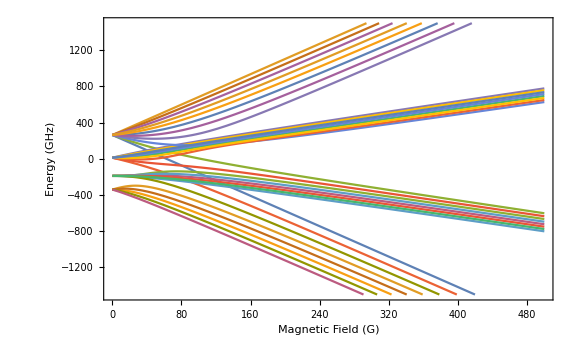

```mathematica
nStatesEs=(2totIEs+1)*(2totJEs+1);
IzEs=DiagonalMatrix[Table[mi,{mi,-totIEs,totIEs}]];
JzEs=DiagonalMatrix[Table[mj,{mj,-totJEs,totJEs}]];
IplusEs=DiagonalMatrix[Table[√(totIEs(totIEs+1)-mi(mi+1)),{mi,-totIEs,totIEs-1}],-1];
IminusEs=Transpose[IplusEs];
JplusEs=DiagonalMatrix[Table[√(totJEs(totJEs+1)-mj(mj+1)),{mj,-totJEs,totJEs-1}],-1];
JminusEs=Transpose[JplusEs];
JxEs=1/2(JplusEs+JminusEs);
JyEs=1/(2I)(JplusEs-JminusEs);
IxEs=1/2(IplusEs+IminusEs);
IyEs=1/(2I)(IplusEs-IminusEs);
JidEs=IdentityMatrix[2totJEs+1];
IidEs=IdentityMatrix[2totIEs+1];
OpOuter[a_,b_]:=Flatten[Outer[Times,a,b],{{1,3},{2,4}}];
IzEs=OpOuter[JidEs,IzEs];
JzEs=OpOuter[JzEs,IidEs];
IxEs=OpOuter[JidEs,IxEs];
JxEs=OpOuter[JxEs,IidEs];
IyEs=OpOuter[JidEs,IyEs];
JyEs=OpOuter[JyEs,IidEs];
HhfsSimpleEs=AhfsEs(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs);
HhfsHigherOrderEs=If[Abs[BhfsEs]>0,BhfsEs((3(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+3/2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)-totIEs(totIEs+1)totJEs(totJEs+1))/(2totIEs(2totIEs-1)totJEs(2totJEs-1)))+ChfsEs(10(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^3+20(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)^2+2(IxEs.JxEs+IyEs.JyEs+IzEs.JzEs)(totIEs(totIEs+1)+totJEs(totJEs+1)+3-3totIEs(totIEs+1)totJEs(totJEs+1))-5totIEs(totIEs+1)totJEs(totJEs+1))/(totIEs(totIEs-1)(2totIEs-1)totJEs(totJEs-1)(2totJEs-1)),0];
HzeemanEs=μB(gJEs JzEs+gI IzEs)Bz;
{evalsEs,evecsEs}=Eigensystem[HzeemanEs+HhfsSimpleEs];
evecsEs=Simplify[Table[evecsEs[[ii]]/Sqrt[Total[Conjugate[evecsEs[[ii]]].evecsEs[[ii]]]],{ii,1,nStatesEs}],Bz∈Reals];
energiesEs=Simplify[Table[Conjugate[evecsEs[[ii]]].(HzeemanEs+HhfsSimpleEs+HhfsHigherOrderEs).evecsEs[[ii]],{ii,1,nStatesEs}],Bz∈Reals];
mIlistEs=Table[IzEs[[ii,ii]],{ii,1,nStatesEs}];mJlistEs=Table[JzEs[[ii,ii]],{ii,1,nStatesEs}];FlistEs=Flatten[Table[Table[F,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mFlistEs=Flatten[Table[Table[mF,{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]];mImJtoFmFEs=Quiet[Transpose[Table[Flatten[Table[Table[ClebschGordan[{totIEs,mIlistEs[[ii]]},{totJEs,mJlistEs[[ii]]},{F,mF}],{mF,-F,F}],{F,totIEs-totJEs,totIEs+totJEs}]],{ii,1,nStatesEs}]]];evecsHighFieldEs=Chop[N[evecsEs/.Bz->10^10],10^-4];
evecsLowFieldEs=Chop[N[evecsEs/.Bz->0],10^-4];
IJcomponentsEs[vec_]:=Module[{max,indmax},
	indmax=Ordering[Abs[vec],-1][[1]];
	{mIlistEs[[indmax]], mJlistEs[[indmax]]}
];
FmFcomponentsEs[vec_]:=Module[{max,indmax,FmFvec},
	FmFvec=mImJtoFmFEs.vec;indmax=Ordering[Abs[FmFvec],-1][[1]];{FlistEs[[indmax]],mFlistEs[[indmax]]}];
{mIhighfieldEs,mJhighfieldEs}=Transpose[Table[IJcomponentsEs[evecsHighFieldEs[[ii]]],{ii,1,nStatesEs}]];
{FlowfieldEs,mFlowfieldEs}=Transpose[Table[FmFcomponentsEs[evecsLowFieldEs[[ii]]],{ii,1,nStatesEs}]];
evecsFmFEs=Table[mImJtoFmFEs.evecsEs[[ii]],{ii,1,nStatesEs}];
Plot[energiesEs, {Bz, 0, 500}, ImageSize -> Large, 
  Frame -> True, FrameLabel -> {"Magnetic Field (G)", "Energy (GHz)"}, 
  PlotRange -> {{0, 500}, {-1500, 1500}}]
```

```mathematica
DipoleMatEl=Table[
Quiet[(-1)^(FlistGs[[ii]] - 1 + mFlistGs[[ii]])*Sqrt[2*FlistGs[[ii]] + 1]*ThreeJSymbol[{FlistEs[[jj]], mFlistEs[[jj]]}, 
       {1, q}, {FlistGs[[ii]], -mFlistGs[[ii]]}]*(-1)^(FlistEs[[jj]] + totJGs + 1 + totIGs)*
      Sqrt[(2*FlistEs[[jj]] + 1)*(2*totJGs + 1)]*SixJSymbol[{totJGs, totJEs, 1}, 
       {FlistEs[[jj]], FlistGs[[ii]], totIGs}]],{ii,1,nStatesGs},{jj,1,nStatesEs},{q,-1,1}];
BranchingRatios[EsInd_,B_]:=Module[{unnorm},
unnorm=Chop[Table[Sum[N[Abs[Sum[evecsFmFGs[[ii,kk]] evecsFmFEs[[EsInd,ll]] DipoleMatEl[[kk,ll,q]]/.Bz->B,{kk,1,nStatesGs},{ll,1,nStatesEs}]^2]],{q,1,3}],{ii,1,nStatesGs}],10^-5];
unnorm(*/Total[unnorm]*)
];
AllBranchingRatios[B_]:=Table[BranchingRatios[ii,B],{ii,1,nStatesEs}]
headersGs=Table[StringTemplate["F=`F` mF=`mF`"][<|"F"->FlowfieldGs[[ii]],"mF"->mFlowfieldGs[[ii]]|>],{ii,1,nStatesGs}];
headersEs=Table[StringTemplate["F'=`F` mF'=`mF`"][<|"F"->FlowfieldEs[[ii]],"mF"->mFlowfieldEs[[ii]]|>],{ii,1,nStatesEs}];
```

```mathematica
TableView[AllBranchingRatios[892]/0.5,Headers->{headersGs,headersEs}, ImageSize->Full,ItemSize->6,HeaderSize->7,AllowedDimensions->{nStatesGs,nStatesEs}]
```

1:eJzFlmlQU2cUhoMUUYIFW6Vg0LJNMSwtxSlJ3U4gbLJJCIIELARCayhUWyWI
ggvECgHUhlaGTRYhSFGWhgqxChVkJCWkQYKokJKGYASB0KGgYqS1P+qfO0zm
DjCeme/Xmec8Z+68893PMvpAUOwKDAZj8eoYvzrz//xXasC84XpTe/x1YZNS
6j2ybN69M0/HU90lYHXI3p5e1YjwWP6WkqDAhC2bn/GoYJ1orhN0M8ozRY2j
C3pOdX4we9Vn+b7D/7XTwk5/vQMXZkXQrvCSvvblV5ntawnYs+z+Z1Pb8z5m
TUDa2go/4nP+a18wZXKw1KtPq78uOo3hIrEAwoMh4JG8UO9rfSDBVBXCA59f
sdPD6uHXvOGzqn3F0b5a50keczyn7Csg5YQ71ujxXdR+pWjzL3F/DAPxqj+B
DjzUvKyg0qiregzOnzY6rzbsQM07ZTZUbk6hA3Wq3Hei0VYrb2G4xcAa2w8D
jyoT5LFK1L564h51mjEJVIF5haNnohC887ZjJu/FURacq8OalIXHd0KL531i
fkIbaj+rb51fQFEb9Mhu4q7nyxG8U048UUVeOHfV2GqT+DoPGKNalQhStqL2
l/l8X7bjRzmMnlSD/xXt+5dY40NBjwLPs6QqfG0Eal8YJzuPLZTAdyeUrEi2
CjXPrvxSbk4VQcMqW6cvqINa+W0QtCMiNghwL2YO1/4cCOd8m95pMe0BLPnR
qg7zBvT5Hgn1jggYhMFiRnesv0grn/5J+tUfjIWAx/BXb2q9BZbTScoBFg26
7h0cdya5ovb7xCijw2RRICk9PspUULXyV/zOCEa4QxB1weBuMw6Zr8UWscjc
JENMAZ3S7rdmT0ci5vOKpLUhRnIQcC44z9YNLbmf7eSFrxyQgEt0Uaqg+AHS
HyM/2zd7C3T505VkWSeiX7LR7VN3PgHKGWsrJqpCUO+XLMzxvFnzANpbC9nH
hiUIHnt6Xr+M5AsTG+aN1mICEP3eII3Y8mEj3IjB7r+4EclrK44mt/WnZArU
+7EGGENk1Pzt+iGP1JpR+Oyc6uiHOKFWvnXNWX+39n6487ZwBKun/b7V6aTb
vn80DB5fvq0/b7n4d8zu1XzSxZViUHRNnYvPFADt4FcuDppdMF40p3DwQL4P
hgNXnLpu2g+XOqqfhkb2LtpP9a7p1t0SAuG8vu2GeG/AJaZmrsxrg8RjZZni
zch8DZLqSsnRvdDi1OfLwfUvef5b99P/pO5VwiH7YE2iFXL+CeumHqZzCLQV
qK2ZPPT5Rlt1Eme9+/YdYE+2IsVeGkO+Z69VkFuz3YB1eHWhSIM+DzXHC6nc
QE+oej4Z0XYyGMHf4H6bESe8C47rmRCaUoHo53bfLvr6TDtk5/bQpHT096FS
IwtnOwsgbcxhZzOIEbxPici67Q4NvGxcr22K2ILou11OCS6kyWHjjYBaWmo7
ar+OhFIcaayEbDEhg3kZfZ7eFZy/x9zKgN89CZzyOr8lz4OdlDunG2oHqr77
Zru5gajn2/JeUCzMGmFS3jX/5JsJ1DxRUaJZY9wM7rq9NvRdCgRvlftR8fxL
AsS9NE8q+DwI0eeQglO98FLYcGTmhfAIF7VfY5REMNmhgCxTY5pU04Tgk3V0
zw7K6iHHUc3udulB9Kn8PevTC0KAiWdkTv2NQ+23k5cYTOYxwDGG0z3rSkLw
NlHiZzk5Kniy7qEii6/9f/MvyI8r6A==

```mathematica
0.357/(1-0.489)
```

0.69863

```mathematica
(* Normalize 55 -> 44 decay and then check that whole table normalizes to 1 *)
(* Check on hydrogen atom *)
(* Check factor on zeeman term *)
(* What excited state has the highest overlap with 44? *)
```